```mathematica
(*Full Maxwell+complex scalar+real kink in planar symmetry (fields depend on t,x)*)ClearAll["Global`*"];
```

```mathematica
(*--------------------PARAMETERS--------------------*)a=1.0;(*kink vacuum*)
lambda=1.0;(*phi self-coupling*)
mphi=Sqrt[2 lambda a^2];
alpha=mphi/2.0;(*kink slope*)
mchi0=0.5;(*bare chi mass parameter m_chi*)
g=1.0;(*coupling M_chi^2=mchi0^2+g phi^2*)
e=0.6;(*electric charge (tuneable)*)
```

```mathematica
(*domain& numerics*)
xmin=-200.0;xmax=200.0;
tmax=200.0;
nx=1001;(*spatial points (increase for convergence)*)(*Note:increase nx and reduce step sizes for convergence tests.*)
```

```mathematica
(*sponge/damping near boundaries to absorb outgoing radiation*)dampWidth=30.0;
gammaMax=0.18;
gammaProfile[x_]:=Module[{left,right},left=If[x<xmin+dampWidth,gammaMax*((xmin+dampWidth-x)/dampWidth)^2,0];
right=If[x>xmax-dampWidth,gammaMax*((x-(xmax-dampWidth))/dampWidth)^2,0];
Max[left,right]];
```

```mathematica
(*--------------------HELPER FUNCTIONS--------------------*)phiK[x_,X0_]:=a*Tanh[alpha*(x-X0)];
phiKp[x_,X0_]:=D[phiK[y,X0],y]/. y->x;

VprimePhi[phi_]:=lambda*phi*(phi^2-a^2);(*dV/dphi*)
M2phi[phi_]:=mchi0^2+g*phi^2;(*M_chi^2*)

(*shape mode (for diagnostics):optional*)
psi1xi[ξ_]:=Sqrt[(3 mphi)/4]*Sinh[alpha*ξ]/(Cosh[alpha*ξ]^2);
```

```mathematica
(*--------------------INITIAL DATA--------------------*)Xk0=-20.0;(*kink center initial*)(*chi wavepacket on left moving toward+x*)
Achi=0.03;(*wavepacket amplitude*)
k0=1.5;(*carrier wavenumber*)
omega0=Sqrt[k0^2+mchi0^2];(*approximate carrier freq initially (mass in vacuum)*)
sigma=8.0;
x0packet=xmin+40.0;

(*initial phi:kink*)
phiInit[x_]:=phiK[x,Xk0];

(*initial chi (complex) as u+i v*)
chiInit[x_]:=Achi*Exp[-(x-x0packet)^2/(2 sigma^2)]*Exp[I*k0*(x-x0packet)];
uInit[x_]:=Re[chiInit[x]];
vInit[x_]:=Im[chiInit[x]];

(*initial time derivative for chi chosen to make right-moving wave~exp(i(kx-omega t)):chi_t=-I omega chi*)
uchidotInit[x_]:=Re[-I*omega0*chiInit[x]];
vchidotInit[x_]:=Im[-I*omega0*chiInit[x]];

(*initial gauge fields:choose Lorenz gauge initial conditions consistent and simple*)
(*we set Ax(t=0,x)=0,A0(t=0,x)=0 and choose A0_t and Ax_t to satisfy the Lorenz constraint initially:constraint C=A0_t+Ax_x->pick Ax_x=0 then A0_t=0. (This is a simple consistent choice) More general choices can be constructed by solving elliptic constraints from currents if desired.*)
A0Init[x_]:=0.0;
AxInit[x_]:=0.0;
A0dotInit[x_]:=0.0;
AxdotInit[x_]:=0.0;
```

```mathematica
(*--------------------PDEs (expanded in real components)--------------------*)(*unknowns:phi[t,x],u[t,x],v[t,x],A0[t,x],Ax[t,x]*)(*Use Lorenz gauge;add sponge damping terms (gammaProfile) multiplied by time derivatives to absorb outgoing radiation*)gammaFun[x_]:=gammaProfile[x];

(*Real-imag expansion helpers:u=Re chi,v=Im chi*)
(*Define current components (functions of fields and time derivatives)*)
j0fun[u_,v_,ut_,vt_,A0_]:=2*e*(u*vt-v*ut)-2*e^2*A0*(u^2+v^2);
jxfun[u_,v_,ux_,vx_,Ax_]:=2*e*(u*vx-v*ux)+2*e^2*Ax*(u^2+v^2);

(*PDE system*)
phiEq=D[phi[t,x],{t,2}]-D[phi[t,x],{x,2}]+VprimePhi[phi[t,x]]+(2*g*phi[t,x])*((Re[chi[t,x]])^2+(Im[chi[t,x]])^2)+gammaFun[x]*D[phi[t,x],t]==0;
(*But we will actually code u and v as separate real fields below.*)

(*We'll expand chi PDE into u and v components.Derived from:chi_tt+2 i e A0 chi_t+i e A0_t chi-e^2 A0^2 chi-chi_xx-2 i e Ax chi_x-i e Ax_x chi+e^2 Ax^2 chi+M^2 chi=0 equate real and imaginary parts.*)

(*Build the full system programmatically below inside NDSolveValue setup for clarity.*)
```

```mathematica
(*-----NUMERICAL SOLVE (NDSolveValue)-----*)Print["Preparing to solve the PDE system. This may take some time."];

(*We use NDSolveValue with MethodOfLines spatial discretization.We supply equations for phi,u,v,A0,Ax expanded as reals.*)

(*domain and boundary conditions:-Use Dirichlet far-field values at edges for phi (vacua):phi=+/-a depending on side of kink.-For u,v,set homogeneous Dirichlet (or zero) far away (packet vanishes).-For gauge fields set A0=A x=0 at boundaries (far away potential zero).-Add sponge damping in PDEs via gammaFun multiplied by time derivatives (already included in phi eq).*)

(*Build explicit PDEs for u and v*)
(*Print["0"]*)
uEq=D[u[t,x],{t,2}]-D[u[t,x],{x,2}]
+2*e*(A0[t,x]*D[v[t,x],t]-Ax[t,x]*D[v[t,x],x])
-e*(D[A0[t,x],t]*v[t,x]-D[Ax[t,x],x]*v[t,x])
+(e^2*(Ax[t,x]^2-A0[t,x]^2)+M2phi[phi[t,x]])*u[t,x]
+gammaFun[x]*D[u[t,x],t]==0;

vEq=D[v[t,x],{t,2}]-D[v[t,x],{x,2}]
-2*e*(A0[t,x]*D[u[t,x],t]-Ax[t,x]*D[u[t,x],x])
+e*(D[A0[t,x],t]*u[t,x]-D[Ax[t,x],x]*u[t,x])
+(e^2*(Ax[t,x]^2-A0[t,x]^2)+M2phi[phi[t,x]])*v[t,x]
+gammaFun[x]*D[v[t,x],t]==0;

(*Maxwell equations:wave equations for A0 and Ax with sources j0 and jx*)
j0expr=j0fun[u[t,x],v[t,x],D[u[t,x],t],D[v[t,x],t],A0[t,x]];
jxexpr=jxfun[u[t,x],v[t,x],D[u[t,x],x],D[v[t,x],x],Ax[t,x]];

A0Eq=D[A0[t,x],{t,2}]-D[A0[t,x],{x,2}]-j0expr+gammaFun[x]*D[A0[t,x],t]==0;
AxEq=D[Ax[t,x],{t,2}]-D[Ax[t,x],{x,2}]-jxexpr+gammaFun[x]*D[Ax[t,x],t]==0;

(*phi PDE as explicit expression (use Re[chi] and Im[chi] represented by u and v)*)
phiEq=D[phi[t,x],{t,2}]-D[phi[t,x],{x,2}]+VprimePhi[phi[t,x]]+2*g*phi[t,x]*(u[t,x]^2+v[t,x]^2)+gammaFun[x]*D[phi[t,x],t]==0;

(*Lorenz gauge constraint monitor:C[t,x]=A0_t+Ax_x (should be approx zero)*)
gaugeConstraint[t_,x_]:=D[A0[t,x],t]+D[Ax[t,x],x];

(*Boundary conditions (Dirichlet far-field+absorbing sponge)*)
bcs={phi[t,xmin]==-a,phi[t,xmax]==a,u[t,xmin]==0,u[t,xmax]==0,v[t,xmin]==0,v[t,xmax]==0,A0[t,xmin]==0,A0[t,xmax]==0,Ax[t,xmin]==0,Ax[t,xmax]==0};

(*initial conditions*)
ics={phi[0,x]==phiInit[x],(D[phi[t,x],t]/. t->0)==0.,(*start kink at rest*)u[0,x]==uInit[x],(D[u[t,x],t]/. t->0)==uchidotInit[x],v[0,x]==vInit[x],(D[v[t,x],t]/. t->0)==vchidotInit[x],A0[0,x]==A0Init[x],(D[A0[t,x],t]/. t->0)==A0dotInit[x],Ax[0,x]==AxInit[x],(D[Ax[t,x],t]/. t->0)==AxdotInit[x]};

Print["Solving PDE"];
(*Solve using MethodOfLines with spatial discretization*)
sol=NDSolveValue[{phiEq,uEq,vEq,A0Eq,AxEq,Sequence@@bcs,Sequence@@ics},{phi,u,v,A0,Ax},{t,0,tmax},{x,xmin,xmax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->nx,"MaxPoints"->nx,"DifferenceOrder"->4},"TemporalVariable"->t},MaxSteps->1000,EvaluationMonitor:>Null,AccuracyGoal->6,PrecisionGoal->6];
Print["PDE solve finished."];
```

Preparing to solve the PDE system. This may take some time.

Solving PDE

NDSolveValue::eerri: Warning: estimated initial error on the specified spatial grid in the direction of independent variable x exceeds prescribed error tolerance.

NDSolveValue::mxst: Maximum number of 1000 steps reached at the point t == 140.166.

General::munfl: 3.99416×10^-142 1.5915×10^-167 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.8145×10^-143 4.7386×10^-169 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.51126×10^-145 1.31253×10^-170 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NDSolveValue::eerr: Warning: scaled local spatial error estimate of 5626.27 at t = 140.166 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 1001 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

PDE solve finished.

```mathematica
phi[t,x]/.phi->sol[[1]]
```

InterpolatingFunction[{{0., 140.166}, {-200., 200.}}, <>][t,x]

```mathematica
(*extract functions*)
phiSol[t_,x_]:=Evaluate[phi[t,x]/.phi-> sol[[1]]];
uSol[t_,x_]:=Evaluate[u[t,x]/. u->sol[[2]]];
vSol[t_,x_]:=Evaluate[v[t,x]/. v->sol[[3]]];
A0Sol[t_,x_]:=Evaluate[A0[t,x]/. A0->sol[[4]]];
AxSol[t_,x_]:=Evaluate[Ax[t,x]/. Ax->sol[[5]]];
```

```mathematica
(*-----DIAGNOSTICS:charge,flux,constraint,energy-----*)(*charge density and current functions*)rho[t_,x_]:=2*e*(uSol[t,x]*D[vSol[t,x],t]-vSol[t,x]*D[uSol[t,x],t])-2*e^2*A0Sol[t,x]*(uSol[t,x]^2+vSol[t,x]^2);
jx[t_,x_]:=2*e*(uSol[t,x]*D[vSol[t,x],x]-vSol[t,x]*D[uSol[t,x],x])+2*e^2*AxSol[t,x]*(uSol[t,x]^2+vSol[t,x]^2);

(*Total charge in domain*)
QtotalAtT[tt_]:=NIntegrate[rho[tt,x],{x,xmin,xmax},WorkingPrecision->10,MaxRecursion->20];

(*Charge near wall (integrate around kink center)*)
kinkCenterEstimate[tt_]:=Module[{f,xs,vals,idx},f=Function[{x},phiSol[tt,x]];
xs=Subdivide[xmin,xmax,801];
vals=f/@xs;
idx=FirstPosition[Partition[vals,2,1],{p_,q_}/;p*q<=0,Missing[]];
If[idx===Missing[],(xmin+xmax)/2,xs[[idx[[1]]]]]];

QwallAtT[tt_,width_:20.]:=Module[{Xc=kinkCenterEstimate[tt]},NIntegrate[rho[tt,x],{x,Xc-width,Xc+width},WorkingPrecision->10,MaxRecursion->20]];

(*Boundary fluxes*)
fluxLeftAtT[tt_]:=jx[tt,xmin];
fluxRightAtT[tt_]:=jx[tt,xmax];

(*Gauss constraint residual*)
gaugeResidualAtT[tt_]:=NIntegrate[Abs[D[A0Sol[tt,x],t]+D[AxSol[tt,x],x]],{x,xmin,xmax},WorkingPrecision->8];

(*Energy (field+EM+charged scalar)*)
energyDensity[t_,x_]:=Module[{phit,phix,uit,uix,vit,vix,Efield,Bfield},phit=D[phiSol[t,x],t];phix=D[phiSol[t,x],x];
uit=D[uSol[t,x],t];uix=D[uSol[t,x],x];
vit=D[vSol[t,x],t];vix=D[vSol[t,x],x];
(*EM energy for 1D planar symmetry:E~1/2[(A0_x-A_x_t)^2+(Ax_t-A0_x)^2] but simpler:F_{0x}=A0_x+Ax_t etc.We'll compute EM energy density=1/2(E^2+B^2),approximated by:Ex=-D[A0Sol[t,x],x]-D[AxSol[t,x],t] (electric component along x with our conventions)*)Ex=-D[A0Sol[t,x],x]-D[AxSol[t,x],t];
Em=1/2 Ex^2;(*neglect magnetic components in 1D planar simplification*)(*kinetic+gradient+potential for phi and chi*)ED=1/2 phit^2+1/2 phix^2+(lambda/4)*(phiSol[t,x]^2-a^2)^2;
Echi=1/2 (uit^2+vit^2)+1/2 (uix^2+vix^2)+1/2*M2phi[phiSol[t,x]]*(uSol[t,x]^2+vSol[t,x]^2);
ED+Echi+Em];

EtotalAtT[tt_]:=NIntegrate[energyDensity[tt,x],{x,xmin,xmax},WorkingPrecision->8,MaxRecursion->20];
```

```mathematica
(*-----RUN SOME DIAGNOSTICS (sample times)-----*)timesList=Subdivide[0,tmax,21];

Print["Computing diagnostics (this may take a while)..."];
Qvals=Table[QtotalAtT[tt],{tt,timesList}];
QwallVals=Table[QwallAtT[tt,30.],{tt,timesList}];
fluxL=Table[fluxLeftAtT[tt],{tt,timesList}];
fluxR=Table[fluxRightAtT[tt],{tt,timesList}];
gRes=Table[gaugeResidualAtT[tt],{tt,timesList}];
Evals=Table[EtotalAtT[tt],{tt,timesList}];

Print["Diagnostics done."];

(*quick plots*)
ListLinePlot[{Transpose[{timesList,Qvals}],Transpose[{timesList,QwallVals}]},PlotLegends->{"Total Q","Q near wall"},AxesLabel->{"t","Charge"}]

ListLinePlot[{Transpose[{timesList,fluxL}],Transpose[{timesList,fluxR}]},PlotLegends->{"flux left","flux right"},AxesLabel->{"t","flux"}]

ListLinePlot[Transpose[{timesList,gRes}],AxesLabel->{"t","Gauge residual"},PlotLabel->"Integrated |A0_t + Ax_x|"]

ListLinePlot[Transpose[{timesList,Evals}],AxesLabel->{"t","Energy"},PlotLabel->"Total energy (diagnostic)"]

Print["Final total charge = ",Last[Qvals],", final charge near wall = ",Last[QwallVals]];
Print["Final gauge residual = ",Last[gRes]];
Print["Final energy = ",Last[Evals]];

(*End of script*)
```

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

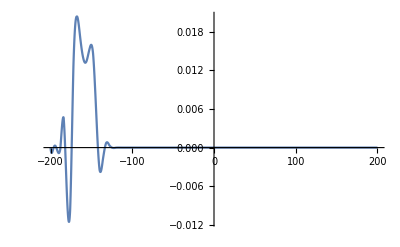

```mathematica
Plot[uSol[60, x], {x, xmin, xmax}, PlotRange->Full]
```

```mathematica
Print["Opening interactive slider (Manipulate). For large nx this may be slower—reduce nx for snappier interactivity."];
Manipulate[Plot[Evaluate[uSol[t0,x]],{x,xmin,xmax},PlotRange->Full,AxesLabel->{"x","ϕ(x,t)"},PlotLabel->Row[{"\!\(\*SubscriptBox[\(ϕ\), \((x,t)\)]\) at t = ",NumberForm[t0,{5,2}]}],ImageSize->Large,PerformanceGoal->"Quality"],{{t0,0,"time t"},0,tmax,Appearance->"Labeled"},ControlPlacement->Top]
```

Opening interactive slider (Manipulate). For large nx this may be slower—reduce nx for snappier interactivity.